```mathematica
NotebookEvaluate[NotebookDirectory[]<>"NOMexplicitPhaseFieldMaiN.nb"];
```

```mathematica
(*Create the model*)
xmin={0.,0.};xmax={0.5,0.5};{width,height}=xmax-xmin;dx= 0.01;
coord3=GridDomain[xmin,xmax,dx];
ktxmin={width/2+dx/2,0.};ktxmax={width ,height/2-dx/2};
coord2=coord3[[FindPoints[coord3,ktxmin,ktxmax]]];coord=Complement[coord3,coord2];h=coord;
Txmin={width/2,0.};Txmax={width/2,height/2};p=FindPoints[coord,Txmin,Txmax];
Txmin1={width/2 ,height/2};Txmax1={width,height/2};r=FindPoints[coord,Txmin1,Txmax1];s=Union[p,r];
mm1=DelaunayMesh[h]; t=Cases[MeshCells[mm1,2],Polygon[x_]:>x,-1];vp=Permutations[s,{3}];
ty=Complement[t,vp];

vol=ConstantArray[dx^2,Length[coord]];
volt=ConstantArray[dx^2,2 Length[coord]];
Nnode=Length[coord];ndim=Length[coord[[1]]];
ndof=ndim Nnode;
Es=25.85 10^9;mu=0.18;rho=7800.;pmass=rho vol;etype=2;
Gc=89.;ls=2dx;pfModulus=4.;pfModulusT=1.;(*phase field length scale.*)
{bulkK,shearG}=PlaneStress[Es,mu,True];
penCoef=1.;
numNei=8;
NeiList=Nearest[coord->Automatic,coord,numNei+1];
WeiF[r_]:=1./r^2;
coord0=coord;mesh1=Abaqus2Mesh[h,ty];(*mesh for postprocess only*)
acc=ConstantArray[0.,{Nnode,ndim}];
accNew=acc;
internalF=acc;
velo=acc;
veloSound=Sqrt[Es/rho];tIncMax=dx/veloSound;
ctime=0.;
tInc=0.8tIncMax;
TotalTime=10 tInc;
pfList=ConstantArray[0.,Nnode];
gradS=ConstantArray[0.,{Nnode,ndim}];lapS=pfList;
bmatrix=ConstantArray[0.,{ndim ndim ,ndim Nnode}];
hgmatrix=ConstantArray[0.,{ndim Nnode,ndim Nnode}];
enerP=pfList;
uvw=0.;
deformList=0.;
```

```mathematica
neicoord0=NeighborPartition[coord0,NeiList];
neivol=NeighborPartition[vol,NeiList];
WeiF[r_]:=1./r^2;
neiWeiL=WeightByNeighbor[neicoord0,WeiF];
{trKList,invKList,vKList, detlist}=KmatrixL[neicoord0,neiWeiL,neivol];
```

```mathematica
nfix=FindPoints[coord,xmin-{0.5 dx,0.5 dx},xmin+{height+0.5 dx,0.5dx}];
nvelo=FindPoints[coord,{0.47,0.25},{0.47,0.25}];
dofFix=ConstantArray[{0.,0.},Length[nfix]];
forceY={0.,10^-8};
dispInc=ConstantArray[forceY,Length[nvelo]];
nforce={};
dofForce={};
xmid=0.5 (xmin+xmax);
```

```mathematica
KineticEnergy={};
timeList={};
strainEnergy={};
pfEnergy={};
uMaxList={};
vMaxList={};
NMaxList={};
reactionForceList={};
Pskt={};
KMat={};
vmat={};
jstep=1;
```

```mathematica
$HistoryLength=1;
```

```mathematica
statisticInterval=5;outputInterval=120;printInterval=120;ls=1.25dx;
numstep=200000;

resiMaxList={};

fpath=CreateFolder[ToString[Gc]<>"tensionV1ls1.25dxTreshold"<>ToString[IntegerPart[width/dx]]];gcl=0.Gc/ls;L2pfresidu=0.;L2pfInc=0.;pfInc=0.;tolL2pfInc=10.^-4;
tolpfIncMax=10.^-3;
resiMaxTol=10.^-2;subInterMax=20;
```

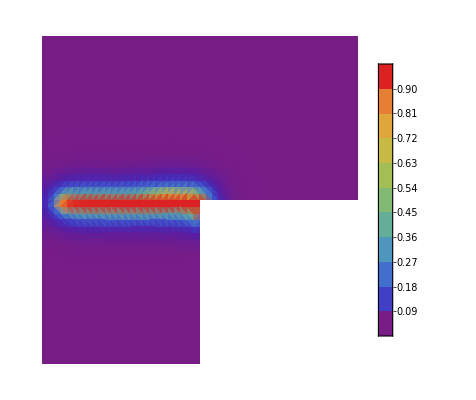

```mathematica
Do[coord+=tInc velo+(0.5 tInc^2)acc;
coord[[nfix]]=coord0[[nfix]]+dofFix;(*displacement constraint*)
coord[[nvelo]]+=dispInc;
velo[[nfix]]=0.;
uvw=coord-coord0;
neicoord=NeighborPartition[coord,NeiList];
neipfList=NeighborPartition[pfList,NeiList];
{gradS,deformList}=FSmatrixL[neipfList,neicoord,neicoord0,neivol,invKList,neiWeiL];
{enerP,enerN,stress,stressP}=StressList[ndim,bulkK,shearG,gcl,deformList];kMax=1;resiMax1=0.;
resiMax2=0.;
Do[
lapS=LaplaceSListAll[NeiList,neicoord0,gradS,neipfList,invKList,trKList,neivol,penCoef,neiWeiL];
lapS/=vol;
pfresi=PhaseFieldResidual[ls,Gc,lapS,pfList,enerP];
If[k==1,resiMax1=Max[pfresi]];
resiMax2=Max[pfresi];
AppendTo[resiMaxList,resiMax2];
L2pfInc=Sqrt[(pfresi vol).pfresi/Total[vol]];
If[k==1,pfModulusT=Max[pfModulus,20 resiMax1]];
pfList+=1./pfModulusT*pfresi;
kMax=k;
If[k==1 && resiMax1<resiMaxTol,Break[]];
If[resiMax2<tolpfIncMax || k==subInterMax,Break[],neipfList=NeighborPartition[pfList,NeiList];gradS=GradSmatrixL[neipfList,neicoord0,neivol,invKList,neiWeiL]];
,{k,1,subInterMax}];
(*Print["subIteration:",kMax," resiMax:",resiMax2," resiMax0:",resiMax1];*)
stress+=((1.-pfList)^2-1.)stressP;
internalF=ForceListAllpf[NeiList,neicoord,neicoord0,stress,deformList,invKList,trKList,neivol,penCoef shearG,neiWeiL,pfList];
internalF[[nforce]]+=dofForce;
accNew=internalF/pmass;
accNew[[nvelo]]=0.;
velo+=0.5 tInc (acc+accNew);
accNew[[nfix]]=0.;
acc=accNew;
ctime+=tInc;jstep++;
If[Mod[jstep,statisticInterval]==1,AppendTo[timeList,ctime];AppendTo[KineticEnergy,0.5 pmass .Table[velo[[i]].velo[[i]],{i,Length[velo]}]];AppendTo[strainEnergy,StrainEnergyCal[enerP,enerN,vol,pfList]];AppendTo[pfEnergy,Gc (PhaseFieldEnergy[pfList,gradS,ls,vol])];
AppendTo[reactionForceList,Total[- internalF[[nvelo]]]];
AppendTo[Pskt,Psk];
  AppendTo[uMaxList,Total[ Max[uvw]]]];
If[Mod[jstep,printInterval]==1,Print["acc max:",Max[accNew],",vel max:",Max[velo],",umax: ",Max[uvw]];
Print["step=",jstep,",t=",ctime," done"];];
CheckTextCommand[isAbortPath];
(*Print[Plot2DField[pfList,mesh1]]*)
If[Max[uvw]>1*10^-3,Break[],{i,numstep}],{i,numstep}];
Plot2DField[pfList,mesh1]
```

```mathematica
SaveToCell[{timeList,uMaxList,resiMaxList,KineticEnergy,strainEnergy,pfEnergy,reactionForceList},"ls=1.25dx,100,1G"]
```

```mathematica
{timeList,uMaxList,resiMaxList,KineticEnergy,strainEnergy,pfEnergy,reactionForceList}="ls=1.25dx,100,1G";
```

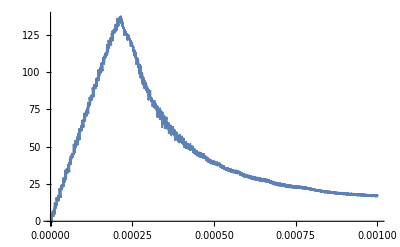

```mathematica
ListPlot[{uMaxList,reactionForceList[[All,2]]/1000}ᵀ]
```